```mathematica
cumulantModel=Sum[cumdist[t,coffs[[1]][[i]],coffs[[2]][[i]],coffs[[3]][[i]],coffs[[4]][[i]]],{i,basdim}]
```

cd[1]/(1+((t-ca[1])/cb[1])^(-cc[1]))+cd[2]/(1+((t-ca[2])/cb[2])^(-cc[2]))

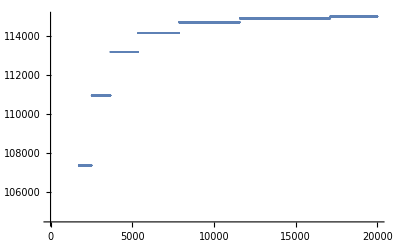

```mathematica
CumStrength=Get["/home/kirscher/kette_repo/ComptonLIT/systems/tmp/CumStrength.plot_57087"];
ListPlot[CumStrength[[All,2]]]
```

```mathematica
cumdist[t_,a_,b_,c_,d_]:=d/(1+((t-a)/b)^(-c));
hea[l_,slop_,loc_,scale_]:=scale loc/(loc+Exp[-slop l]);
(*Animate[
Plot[cumdist[x,a,b,c,d],{x,-1,20000},PlotRange->Full],{a,-5,5,Appearance->"Labeled"},{b,0.1,5,Appearance->"Labeled"},{c,0.001,5,Appearance->"Labeled"},{d,0.001,10.^6,Appearance->"Labeled"},AnimationRunning->False]*)
Animate[
Plot[hea[l,slop,loc,scale],{l,-1,10}],{slop,0.5,5,Appearance->"Labeled"},{loc,0.1,5,Appearance->"Labeled"},{scale,0.1,5,Appearance->"Labeled"},AnimationRunning->False
]
```

(ca[1]^2 cb[1])/(ⅇ^(-t cc[1])+cb[1])+(ca[2]^2 cb[2])/(ⅇ^(-t cc[2])+cb[2])+(ca[3]^2 cb[3])/(ⅇ^(-t cc[3])+cb[3])+(ca[4]^2 cb[4])/(ⅇ^(-t cc[4])+cb[4])+(ca[5]^2 cb[5])/(ⅇ^(-t cc[5])+cb[5])+(ca[6]^2 cb[6])/(ⅇ^(-t cc[6])+cb[6])

{ca[1]→-8.68744×10^-7,ca[2]→337.538,ca[3]→6.31474×10^-21,ca[4]→-3.18412×10^-6,ca[5]→-1.53946×10^-13,ca[6]→5.16433×10^-7,cb[1]→-5166.17,cb[2]→0.244526,cb[3]→938.95,cb[4]→2418.32,cb[5]→-182.844,cb[6]→-4842.18,cc[1]→304.993,cc[2]→0.298995,cc[3]→637.035,cc[4]→607.544,cc[5]→-61.2881,cc[6]→3466.82}

General::munfl: 3.74415×10^-38 2.98635×10^-276 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.29142×10^-9 3.64059891938379×10^-1500 is too small to represent as a normalized machine number; precision may be lost.

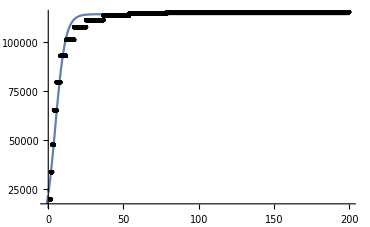

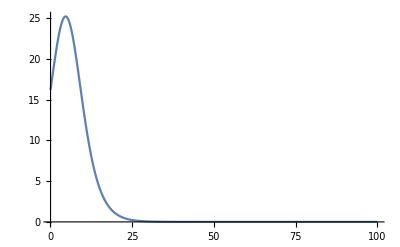

```mathematica
basdim=6;

coffs={Array[ca,basdim],Array[cb,basdim],Array[cc,basdim]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.01,1.2},Length[Flatten[coffs]]]}];

model2=Sum[coffs[[1]][[i]]^2 coffs[[2]][[i]]/(coffs[[2]][[i]]+Exp[-coffs[[3]][[i]] t]),{i,basdim}]
data=CumStrength;

optPOSsol=FindFit[data,model2,inicoffs,t]
expan[x_]:=model2/.optPOSsol/.t->x
Plot[expan[t],{t,-1,CumStrength[[-1,1]]},Epilog->Map[Point,CumStrength],PlotRange->Full]
model2de=Sum[coffs[[1]][[i]] coffs[[2]][[i]] coffs[[3]][[i]] Exp[-coffs[[3]][[i]] t]/(coffs[[2]][[i]]+Exp[-coffs[[3]][[i]] t])^2,{i,basdim}]/.optPOSsol;
strength[e_]:=model2de/.t->e;
Plot[strength[ee],{ee,0.1,100},PlotRange->Full]
```

c0+ⅇ^(-t c2exp[1]) c1exp[1]+ⅇ^(-t c2exp[2]) c1exp[2]+ⅇ^(-t c2exp[3]) c1exp[3]+ⅇ^(-t c2exp[4]) c1exp[4]+(t cnum[1]+t^2 cnum[2]+t^3 cnum[3]+t^4 cnum[4])/(cdenom[1]+t cdenom[2]+t^2 cdenom[3]+t^3 cdenom[4])

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{c0→-3.32027,cnum[1]→1.17117,cnum[2]→9.9552,cnum[3]→1.0804,cnum[4]→-0.0000484354,cdenom[1]→0.000529485,cdenom[2]→0.000346334,cdenom[3]→0.0000918968,cdenom[4]→9.28374×10^-6,c1exp[1]→3.87764,c1exp[2]→-0.0961136,c1exp[3]→3.93514,c1exp[4]→-4.39638,c2exp[1]→6.43455,c2exp[2]→0.201093,c2exp[3]→9.54921,c2exp[4]→8.15712}

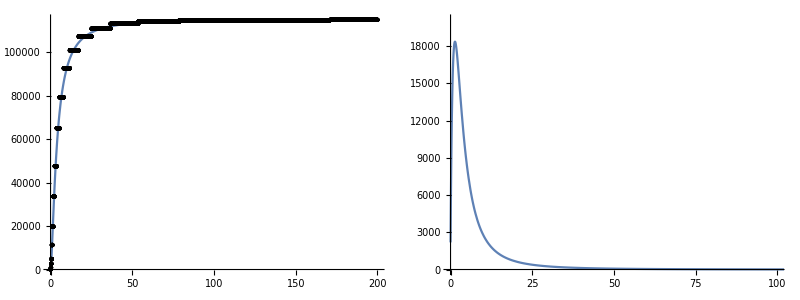

-3.32027+3.93514 ⅇ^(-9.54921 σ)-4.39638 ⅇ^(-8.15712 σ)+3.87764 ⅇ^(-6.43455 σ)-0.0961136 ⅇ^(-0.201093 σ)+(1.17117 σ+9.9552 σ^2+1.0804 σ^3-0.0000484354 σ^4)/(0.000529485+0.000346334 σ+0.0000918968 σ^2+9.28374×10^-6 σ^3)

```mathematica
ordnum=4;orddenom=4;ordexp=4;
coffs={c0,Array[cnum,ordnum],Array[cdenom,orddenom],Array[c1exp,ordexp],Array[c2exp,ordexp]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.01,10.2},Length[Flatten[coffs]]]}];

num=Sum[coffs[[2]][[n]] t^n,{n,ordnum}];
denom=Sum[coffs[[3]][[n+1]] t^n,{n,0,orddenom-1}];
expo=Sum[coffs[[4]][[n]] Exp[-coffs[[5]][[n]] t],{n,ordexp}];
model=coffs[[1]]+num/denom+expo
CumStrength=Get["/home/kirscher/kette_repo/ComptonLIT/systems/tmp/CumStrength.plot_57087"];
data=CumStrength;

optPOSsol=FindFit[data,{model,coffs[[3]][[1]]>0,Total[coffs[[4]]]+coffs[[1]]==0},inicoffs,t,MaxIterations->1000,PrecisionGoal->10,AccuracyGoal->10,Method->Automatic]
expan[x_]:=model/.optPOSsol/.t->x
strength[x_]:=D[expan[t],t]/.t->x
Grid[{{Plot[expan[t],{t,0,CumStrength[[-1,1]]},Epilog->Map[Point,CumStrength],PlotRange->Full,ImageSize->500],Plot[strength[ee],{ee,0,CumStrength[[-1,1]]},PlotRange->{{0,100},{0,20100}},ImageSize->500]}}]
expan[σ]
strength[t];
```